```mathematica
init = CenterArray[1,50];
```

```mathematica
CellularAutomaton[110, init, 50]//ArrayPlot
```

-Graphics-

```mathematica
NestWhile[
CellularAutomaton[1, #, 50]&,
init,
!MemberQ[#, CellularAutomaton[1, Last@#]]&,
All
]
```

CellularAutomaton::initn: The initial condition specification 0 should be of the form aspec, {aspec, bspec}, or {{{aspec1, off1}, {aspec2, off2},... {aspecn, offn}}, bspec} (n > 0). Each aspec must be a non-empty rank 1 array whose elements at level 1 are integers i in the range 0 <= i <= 1.

CellularAutomaton::initn: The initial condition specification {{0,0,0,0,0,0,0,0,0,0,«40»},{1,1,1,1,1,1,1,1,1,1,«40»},{0,0,0,0,0,0,0,0,0,0,«40»},{1,1,1,1,1,1,1,1,1,1,«40»},{0,0,0,0,0,0,0,0,0,0,«40»},{1,1,1,1,1,1,1,1,1,1,«40»},{0,0,0,0,0,0,0,0,0,0,«40»},{1,1,1,1,1,1,1,1,1,1,«40»},{0,0,0,0,0,0,0,0,0,0,«40»},{1,1,1,1,1,1,1,1,1,1,«40»},«41»} should be of the form aspec, {aspec, bspec}, or {{{aspec1, off1}, {aspec2, off2},... {aspecn, offn}}, bspec} (n > 0). Each aspec must be a non-empty rank 1 array whose elements at level 1 are integers i in the range 0 <= i <= 1.

General::stop: Further output of CellularAutomaton::initn will be suppressed during this calculation.

$Aborted

```mathematica
CellularAutomaton[1,init,50]//ArrayPlot
```

-Graphics-

```mathematica
CellularAutomaton[1, init]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
states={%, CellularAutomaton[1,%]}
```

{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

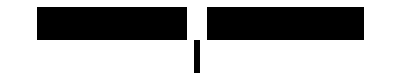

```mathematica
ArrayPlot@states
```

```mathematica
MemberQ[states, CellularAutomaton[1,Last@states]]
```

True